## 1.) Aproksimacija števila π

```mathematica
Get["C:\\Users\\jakob\\Desktop\\3.letnik\\Napredna računalniška orodja\\Wolfram Matematica\\MonteCarloPi.m"]
```

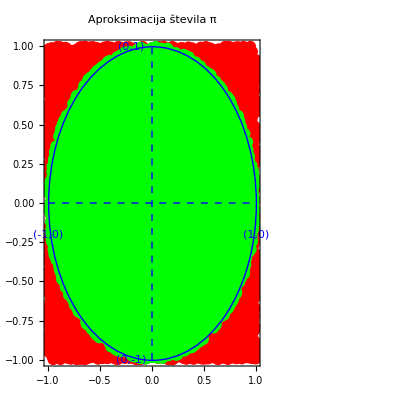

π_aproksimacija=3.1512

```mathematica
MonteCarloPi[1000000]
```

## 2.) Razvoj v Taylorjevo vrsto

```mathematica
funkcija1[t_]=Sin[t]  t^2  Exp[-t];

funkcija2=Normal[Table[Series[funkcija1[t],{t,2,n}],{n,0,15}]];

Manipulate[Plot[{funkcija1[t],funkcija2[[r]]},{t,0,4},
AxesLabel->{"t","f[t]"},
PlotStyle->{Green,Red},
PlotLegends->{"sin(t) t^2 e^-t",StringForm["Taylorjeva vrsta reda ``.",r-1]}],
{r,1,11,1}]
```